```mathematica
f[x_]=(x^3-5x^2+3x+1)/(2x^2+x-1)
```

(1+3 x-5 x^2+x^3)/(-1+x+2 x^2)

```mathematica
g[x_]=Log[(x^2-1)/(2x-3)]
```

Log[(-1+x^2)/(-3+2 x)]

```mathematica
h[x_]=Sin[x/3]-cos[x^3/5]
```

-cos[x^3/5]+Sin[x/3]

```mathematica
Solve[f[x]==0,x]
```

{{x→1},{x→2-√5},{x→2+√5}}

```mathematica
f[x]
```

(1+3 x-5 x^2+x^3)/(-1+x+2 x^2)

```mathematica
Reduce[f[x]>0,x]
```

-1<x<2-√5||1/2<x<1||x>2+√5

```mathematica
f'[x]
```

(3-10 x+3 x^2)/(-1+x+2 x^2)-((1+4 x) (1+3 x-5 x^2+x^3))/((-1+x+2 x^2)^2)

```mathematica
Reduce[f'[x]>0,x]
```

x<Root[1-#1+3 #1^2+#1^3&,1]||x>2

```mathematica
N[%]
```

x<-3.38298||x>2.

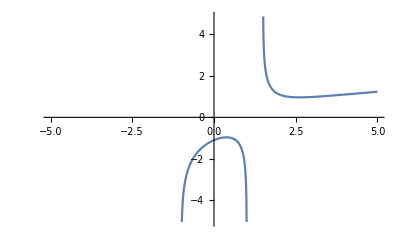

```mathematica
Plot[g[x],{x,-5,5}]
```

```mathematica
Solve[(x^2-1)/(2x-3)==0,x]
```

{{x→-1},{x→1}}

```mathematica
Solve[g'[x]== 0,x]
```

```mathematica
{{x->1/2 (3-√5)},{x->1/2 (3+√5)}}
```

{{x→1/2 (3-√5)},{x→1/2 (3+√5)}}

```mathematica
N[%]
```

{{x→0.381966},{x→2.61803}}

```mathematica
g[1/2 (3-√5)]
```

```mathematica
Simplify[Log[-(-1+1/4 (3-√5)^2)/(√5)]]
```

Log[1/2 (3-√5)]

```mathematica
Simplify[g[1/2 (3+√5)]]
```

Log[1/2 (3+√5)]

```mathematica
Plot[h[x],{x,1,3}]
```

-Graphics-

```mathematica
h[x]
```

```mathematica
-cos[x^3/5]+Sin[x/3]
```

-cos[x^3/5]+Sin[x/3]

```mathematica
FindRoot[h[x],{x,1.5}]
```

FindRoot::nlnum: The function value {0.479426-1. cos[0.675]} is not a list of numbers with dimensions {1} at {x} = {1.5}.

```mathematica
FindRoot[h[x],{x,2.5}]
```

FindRoot::nlnum: The function value {0.740177-1. cos[3.125]} is not a list of numbers with dimensions {1} at {x} = {2.5}.

```mathematica
FindRoot[h'[x],{x,2.5}]
```

FindRoot::nlnum: The function value {0.224137-3.75 cos'[3.125]} is not a list of numbers with dimensions {1} at {x} = {2.5}.

```mathematica
FindRoot[h'[x],{x,2.5}]
```

Syntax::sntxi: Incomplete expression; more input is needed .